## Core parameters

```mathematica
α=1;β=2;γ=.;u=0;
q1=1;q2=1.5;q3=.;
```

```mathematica
cols=ColorData[97,"ColorList"]⟦{2,1,3}⟧
```

{RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.560181, 0.691569, 0.194885]}

## Dynamic γ

```mathematica
G=0.1;ginit=0.4;
q={q1,q2};
sampleinits={0.2,0.4,0.6,0.8};
```

```mathematica
dy1[y1_,γ_]:=y1 (1-y1)((1-γ) q⟦1⟧/(q⟦1⟧+q⟦2⟧)+γ α y1^β/(y1^β+(1-y1)^β) q1 -( (1-γ) q⟦2⟧/(q⟦1⟧+q⟦2⟧)+γ α (1-y1)^β/((1-y1)^β+y1^β)) q2);
```

```mathematica
sol[y1init_,Gon_]:=NDSolve[{y1'[t]==dy1[y1[t],g[t]],(*g evolves according to dg*)g'[t]==If[Gon==True,If[dy1[y1[t],g[t]]==0,0, -1  Sign[dy1[y1[t],g[t]]] G ],0],(*initial conditions*)y1[0]==y1init,g[0]==ginit},{y1,g},{t,0,100}];
```

```mathematica
sol[0.8,False]
```

{{y1→InterpolatingFunction[…],g→InterpolatingFunction[…]}}

NDSolve::ndsz: At t == 52.5623, step size is effectively zero; singularity or stiff system suspected.

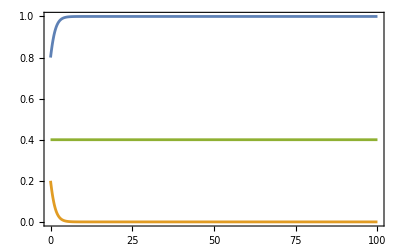
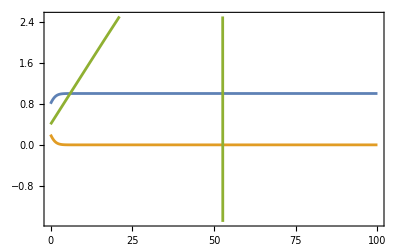
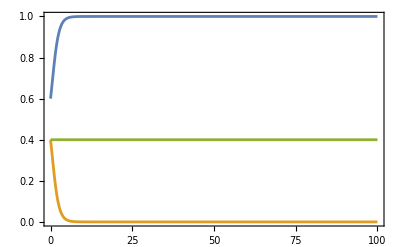
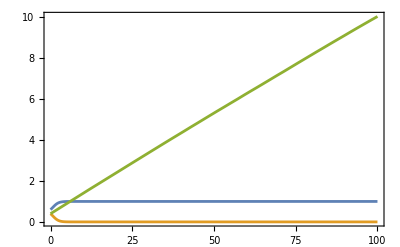
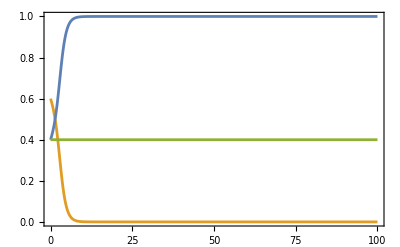
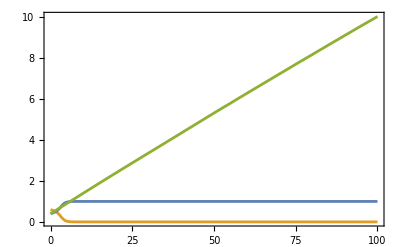
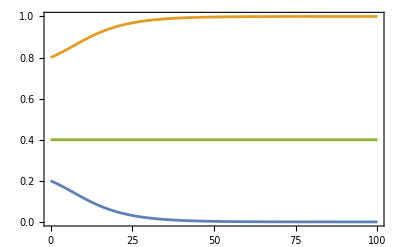
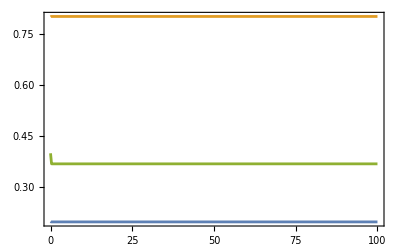

```mathematica
Table[{Plot[Evaluate[{y1[t],1-y1[t],g[t]}/.sol[sampleinits⟦i⟧,False]],{t,0,100},PlotStyle->Join[cols,{Gray}],Frame->True,FrameStyle->Directive[Thickness[0.003]]],
Plot[Evaluate[{y1[t],1-y1[t],g[t]}/.sol[sampleinits⟦i⟧,True]],{t,0,100},PlotStyle->Join[cols,{Gray}],Frame->True,FrameStyle->Directive[Thickness[0.003]]]},{i,1,Length[sampleinits],1}]
```